# Notes (MATH152, 2017-08-30)

∫ⅆu/u=ln|u|+ C

∫x/(x^2+1)ⅆx
u=x^2+1
ⅆu=2x ⅆx, 1/2 ⅆu=xⅆx
1/2∫ⅆu/u=1/2 ln|x^2+1|+ C
=ln √(x^2+1)+C
=ln √(x^2+1)+ln k
=ln k·√(x^2+1)

(∫_1^e (ln x)/x ⅆx=∫_1^e ln x·1/xⅆx(⟶_(ⅆu =1/x ⅆx))^(u=ln x)∫_0^1 uⅆu=1/2 u^2])_0^1=1/2

∫tan x ⅆx=∫(sin x)/(cos x)ⅆx(⟶_(-ⅆu=sin xⅆx)-∫ⅆu/u)^(u=cos x)=-ln|u|+C=-ln|cos x|+C
=ln|cos x|^-1+C=ln |1/(cos x)|+C=ln|sec x|+C

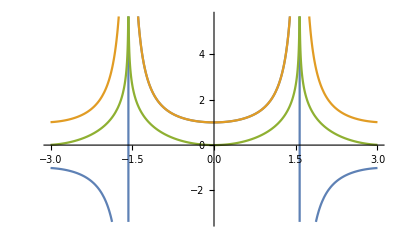

```mathematica
Plot[{Sec[x],Abs[Sec[x]],Log[Abs[Sec[x]]]},{x,-3,3}]
```

ⅆ/ⅆx log_ax=ⅆ/ⅆx(ln x)/(ln a)=1/(x·ln a)=(ln e)/(x·ln a)=(log_a e)/x
e.g.
ⅆ/ⅆx log_102+sin x=(cos x)/(ln 10·(2+sin x))

ⅆ/ⅆx a^x=lim_(h→0) (a^h-1)/h=a^x·l(a) 
ⅆ/ⅆx a^x=ⅆ/ⅆx(e^(ln a))^x=ⅆ/ⅆx e^(x·ln a)=e^(x·ln a)·ln a=a^x·ln a

ln(a)=lim_(h→0) (a^h-1)/h

ⅆ/ⅆt=n_0 2^t=n_o ...

ⅆ/ⅆx 10^(x^2)=2x·10x^2·ln 10

∫a^x ⅆx=a^x/(ln a)+C

y=(x^(3/4)√(x^2+1))/(3x+2)^5

```mathematica
f[x_]:=(x^(3/4)√(x^2+1))/(3x+2)^5; Factor[D[f[x],x]]
```

-(-6+51 x-14 x^2+39 x^3)/(4 x^(1/4) (2+3 x)^6 √(1+x^2))

ln y=ln(x^(3/4)√(x^2+1))/(3x+2)^5
=ln x^(3/4)+ln √(x^2+1)-ln(3x+2)^5
=3/4 ln x+1/2 ln(x^2+1)-5ln(3x+2)

ⅆy/ⅆx 1/y=3/(4x)+(2x)/(2(x^2+1))-15/(3x+2)
ⅆy/ⅆx=(3/(4x)+x/(x^2+1)-15/(3x+2))(x^(3/4)√(x^2+1))/(3x+2)^5

(This really only works if y>0 — if it’s not, take the absolute value, “as we’ll see later?”)

## Proof.

ⅆ/ⅆx x^n∀n∈ℝ

y=x^n
|y|=|x^n|
ln|y|=ln|x^n|=^(because x is always positive)ln|x|^n=n·ln|x|

ⅆy/ⅆx 1/y=n·1/x⇒ⅆy/ⅆx=(n·x^n)/x=n·x^(n-1)

ⅆ/ⅆx b^a=0

ⅆ/ⅆx f(x)^a=a·f(x)^(a-1)·ⅆ/ⅆx f(x)

ⅆ/ⅆx b^(g(x))=b^(g(x))·ⅆ/ⅆx g(x)·ln b
ⅆ/ⅆx f(x)^(g(x))⟹use log diff.

y=x^(√x),x>0
ln y=ln x^(√x)=√x ln x
ⅆy/ⅆx 1/y=(√x)/x+(ln x)/(2 √x)=(2+ln x)/(2 √x)
ⅆy/ⅆx=(2+ln x)/(2 √x)·x^(√x)

ⅆ/ⅆx x^(√x)=ⅆ/ⅆx e^(ln x^(√x))=ⅆ/ⅆx e^(√x ln x)=e^(√x ln x)·((2+ln x)/(2 √x))
= x^(√x)((2+ln x)/(2 √x))

f(x)=ln x⟹f'(x)=1/x
f'(1)=1/1=1
1=f'(1)=lim_(h→0) (f(1+h)-f(1))/h=lim_(h→0) (f(1+h)-0)/h
=lim_(h→0) (ln(1+h))/h=lim_(h→0) ln(1+h)^(1/h)
e=e^(lim_(h→0) ln(1+h)^(1/h))⟹^(n=1/h)e=lim_(n→∞) (1+1/n)^n